```mathematica
<<Units`
```

```mathematica
Convert[9.81 Meter/Second^2,1 Inch/Second^2 ] 
Convert[1Pound/Gallon,1 Pound/Inch^3 ] Convert[1Feet,1Inch]
```

(386.22 Inch)/Second^2

(0.0519481 Pound)/Inch^2

```mathematica
ppgfttoPSI=0.0519481
```

0.0519481

```mathematica
MakeCompatibleSizeVectors[refinedvec_,coarsevecl_,coarsevecvar_]:=Block[{newvec,y0,y1,x0,x1,counter,i},
newvec={};
counter=1;
If[Length[coarsevecl]!=Length[coarsevecvar],
Print["Não é possível realizar o refinamento, os vetores coarse devem ter o mesmo tamanho."];
];
For[i=1,i<Length[coarsevecl],i++,
(*If[i>=Length[coarsevecvar],Break[]];*)
y0=coarsevecvar[[i]];
y1=coarsevecvar[[i+1]];
x0=coarsevecl[[i]];
x1=coarsevecl[[i+1]];
While[(coarsevecl[[i]]<=refinedvec[[counter]]<=coarsevecl[[i+1]])&&counter<Length[refinedvec],
AppendTo[newvec,(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0];
counter++;
];
If[i==Length[coarsevecl]-1,AppendTo[newvec,(y1-y0)/(x1-x0) (refinedvec[[counter]]-x0)+y0]];
];
newvec
]
```

```mathematica
(*refina de n divisões de refl até lf*)
refine[l0_,lf_,refl_,n_]:=Block[{dref,standardref=100,refinedvec,lastcoarsedata,i},
refinedvec=Table[dl//N,{dl,l0,refl,(refl-l0)/standardref}];
lastcoarsedata=refl;
If[Abs[lf-refl]<10^-8,
dref=(lf-l0)/n;
refinedvec={};
lastcoarsedata=l0;
,
dref=(lf-refl)/n;
lastcoarsedata=refl;
];

For[i=1,i≤n,i++,
AppendTo[refinedvec,lastcoarsedata//N];
lastcoarsedata+=dref;
];
AppendTo[refinedvec,lf];
refinedvec
]
```

```mathematica
L0=0.;
LF=14800.;
LtoRef=14799;
nrefs=50.;
refinedl=refine[L0,LF,LtoRef,nrefs];
```

```mathematica
Length[refinedl]
```

152

Dado PI e PO, rint e rext, faz o cálculo da tensão radial e tangencial

```mathematica
ComputeRadialAndTangetialStress[r_,ri_,re_,PI_,PO_]:=Block[{sigr,sigtheta},
sigr=(PI (r^2-re^2) ri^2+PO re^2 (-r^2+ri^2))/(r^2 (re^2-ri^2));
sigtheta=(PI(r^2+re^2) ri^2-PO re^2 (r^2+ri^2))/(r^2 (re^2-ri^2));
{sigr,sigtheta}
];
ComputeRadialAndTangetialStress2[r_,ri_,re_,PI_,PO_,FZ_]:=Block[{ez,sigrr,sigtt,sigzz,a,b,Pa,Pb,nu=0.30,young=3 10^7},
a=ri;
b=re;
Pa=PI;
Pb=PO;
ez=FZ/(Pi young(b^2-a^2))-(2nu)/young(Pa a^2 -Pb b^2)/(b^2-a^2);
sigrr=(Pa a^2 -Pb b^2)/(b^2-a^2)-(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigtt=(Pa a^2 -Pb b^2)/(b^2-a^2)+(a^2 b^2 (Pa-Pb))/((b^2-a^2)r^2);
sigzz=2 nu (Pa a^2 -Pb b^2)/(b^2-a^2)+young ez;
{sigrr,sigtt,sigzz}
];
(*di=12.376;
de=14;
{sigr,sigt,sigz}=ComputeRadialAndTangetialStress2[di/2 ,di/2,de/2,8237,3629,1.312705856587157*^6]
sigz Pi/4( de^2-di^2)*)
```

Dado dint, dext, PI e PO, faz o cálculo da tensão axial (TA) devido ao efeito poisson (Balão)

```mathematica
ComputeFballoning[di_,de_,Pint_,Pext_,nu_]:=Block[{sigr,sigt,Fballoning},
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2 ,di/2,de/2,Pint,Pext];
Fballoning=nu(sigr+sigt)Pi/4( de^2-di^2);
Fballoning
];
```

```mathematica
ComputeFtemperature[de_,di_,TM_,TPM_]:=Block[{young = 3 10^7,alfa=6.9 10^-6,ΔT,T1,f,fp,T2,Ftemperature},
ΔT= (TPM-TM) ;
Ftemperature=-young alfa ΔT Pi/4(de^2-di^2);
Ftemperature
]
```

```mathematica
ComputeInitialForce[InternalPressIni_,ExternalPressIni_,Lvec_,PipeData_]:=Block[{Lcement,Fpiston,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Fi},
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[Lvec];
Fi=Table[0,{sz}];
Fpiston=(InternalPressIni[[sz]] Ai-ExternalPressIni[[sz]] Ao);
Fi[[sz]]=Fpiston;
For[i=sz-1,i≥1,i--,
lacum+=(-Lvec[[i]]+Lvec[[i+1]]);
Fi[[i]]=Fpiston+w lacum;
];

Fi
]
```

```mathematica
ComputeForces[InternalPressinitial_,ExternalPressinitial_,InternalPressKick_,ExternalPressKick_,Ti_,Tf_,Lvec_,PipeData_]:=Block[{Lcement,Fi,Fballoning,Ftemp,flag,Ffreemean,sz,di,de,alfa,nu,young,w,Ai,Ao,i,lacum=0.,Ffinal,ΔInternalPress,ΔExternalPress},
(*Calcula a força devido as condições iniciais*)
Fi=ComputeInitialForce[InternalPressinitial,ExternalPressinitial,Lvec,PipeData];
ΔInternalPress=InternalPressKick-InternalPressinitial;
ΔExternalPress=ExternalPressKick-ExternalPressinitial;
{di,de,alfa,nu,young,w,Lcement}=PipeData;
Ai=Pi/4 di^2;
Ao=Pi/4 de^2;
sz=Length[ΔInternalPress];
Ffreemean=0.;
(*Calcula a força devido ao efeito poisson ou balão*)
Fballoning=Table[ComputeFballoning[di,de,ΔInternalPress[[i]],ΔExternalPress[[i]],nu],{i,1,sz}];
(*Calcula a força devido ao efeito térmico*)
Ftemp=Table[ComputeFtemperature[de,di,Ti[[i]],Tf[[i]]],{i,1,sz}];
Ffinal=Table[0,{sz}];
Ffinal[[sz]]=Fi[[sz]]+Fballoning[[sz]]+Ftemp[[sz]];
For[i=sz-1,i≥1,i--,
lacum+=Lvec[[i+1]]-Lvec[[i]];
If[lacum-(Lvec[[sz]]-Lcement)<=0,
(*Trecho Cimentado*)
Ffinal[[i]]=Fi[[i]]+Fballoning[[i]]+Ftemp[[i]];
flag=True;
,
(*Trecho Livre*)
If[flag==True,
(*No primeiro passo do trecho livre calcula a média das forças de temperatura e balão somente do trecho livre*)
Ffreemean=(Sum[Fballoning[[j]],{j,1,i}]+Sum[Ftemp[[j]],{j,1,i}])/i;
flag=False;
];
Ffinal[[i]]=Ffreemean+Fi[[i]];
];

];

{Fi,Ffinal}
]
```

Calcula a resistência do tubular à ruptura e ao colapso de acordo com a API BUL 5C3

```mathematica
ComputePipeStrength[siga_,sigy_,de_,di_,young_,nu_]:=Block[{t=(de-di)/2,BurstStrength, ColapseStrength,dt,Ypa,A,B,C,F,G,range1,range2,range3},
BurstStrength=0.875 2 sigy/(de/t);
dt=de/t;
Ypa=sigy (Sqrt[1-3/4 (siga/sigy)^2]-1/2 siga/sigy);
A=2.8762+0.10679 10^-5 Ypa+0.21301 10^-10 Ypa^2-0.53132 10^-16 Ypa^3;
B=0.026233+0.50609 10^-6 Ypa;
C=-465.93+0.030867 Ypa-0.10483 10^-7 Ypa^2+0.36989 10^-13 Ypa^3;
F=(46.95 10^6 ((3(B/A))/(2+B/A))^3)/(Ypa((3(B/A))/(2+B/A)-B/A)(1-(3(B/A))/(2+B/A))^2);
G=F B/A;
range1=(2+B/A)/(3 B/A);

If[dt≥ range1,

ColapseStrength=(2 young)/(1-nu^2) 1/(dt(dt-1)^2);
];
range2=(Ypa(A-F))/(C+Ypa(B-G));
If[range2≤ dt≤ range1,

ColapseStrength= (F/dt-G)Ypa;
];
range3=(Sqrt[(A-2)^2+8(B+C/Ypa)]+(A-2))/(2(B+C/Ypa));
If[(range3≤ dt≤ range2),

ColapseStrength=Ypa (A/dt-B)-C;
];

If[dt≤ range3,

ColapseStrength=2Ypa (dt-1)/dt^2;
];
{BurstStrength,ColapseStrength}
];
```

Calcula a tensão de von Mises

```mathematica
ComputeVonMises[sigr_,sigt_,siga_]:=Block[{sig,S,J2},
sig={{sigr,0,0},{0,sigt,0},{0,0,siga}};
S=sig-1/3 Tr[sig] IdentityMatrix[3];
(*Print[S];*)
J2=1/2 Tr[S.S];
Sqrt[3 J2]
];
```

1.3 Pressão resistente de Klever Stewart

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
pfactorNeck=√((1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)));
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
If[sa/fu≤ ((√3)/2)^(1-n),
If[pM≤ (pM+0.5^n puts)/2,
pburst=po+pM;
,
pburst= po+(pM+0.5^n puts)/2;
],
pburst=po+pref*pfactorNeck;
];
pburst
];
```

1.3 Pressão resistente de Klever Tamano

```mathematica
ComputeColapseResistance[siga_,sigy_,pi_,d_,t_,young_,nu_]:=Block[{ke=1,sol,H=0.22,deltapec,deltapy,deltapmises,deltaptresca,ky=1,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},
deltaptresca=ky 2 sigy t/(d-t);
deltapmises=Sqrt[(ky(4/√3)sigy t/(d-t))^2 (1-(siga/(ky sigy))^2)];
(*deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];*)
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
deltapec=ke (2 young)/(1-nu^2)1/((d/t)(d/t-1)^2);
ColapseStrength=pi+(2 deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4 H deltapy deltapec]);
ColapseStrength

]
```

Calcula os fatores de segurança

```mathematica
ComputeSafetyFactors[PipeData_,AxialForce_,Pint_,Pext_]:=Block[{KTStress,KSstress,KSSF={},KTSF={},APISF={}, BarlowSF={},i,barlow,api,de,di,young,nu,weigthperfeet,L1,L2,pipe=1,sigy,VMSF={},sigr,sigt,area,VMStress},

{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
For[i=Length[Pint]-1,i>1,i--,
If[L1>Pint[[i,2]],
pipe++;
{de,di,young,nu,weigthperfeet,L1,L2,sigy}=PipeData[[pipe]];
];
{sigr,sigt}=ComputeRadialAndTangetialStress[di/2,di/2,de/2,Pint[[i,1]],Pext[[i,1]]];
area=Pi/4 (de^2 -di^2);
VMStress=ComputeVonMises[sigr,sigt,AxialForce[[i,1]]/area];
KSstress=ComputeBurstResistance[1,de,0.5(de -di),sigy,AxialForce[[i,1]]/area,Pext[[i,1]]];
KTStress=ComputeColapseResistance[AxialForce[[i,1]]/area,sigy,Pint[[i,1]],de,0.5(de -di),young,nu];
api=ComputePipeStrength[AxialForce[[i,1]]/area,sigy,de,di,young,nu];
AppendTo[BarlowSF,{api[[1]]/(Pint[[i,1]]-Pext[[i,1]]),-Pint[[i,2]]}];
AppendTo[APISF,{api[[2]]/(Pext[[i,1]]-Pint[[i,1]]),-Pint[[i,2]]}];
AppendTo[VMSF,{sigy/VMStress,-Pint[[i,2]]}];
AppendTo[KSSF,{KSstress/(Pint[[i,1]]-Pext[[i,1]]),-Pint[[i,2]]}];
AppendTo[KTSF,{KTStress/(Pext[[i,1]]-Pint[[i,1]]),-Pint[[i,2]]}];
];
{BarlowSF,APISF,VMSF,KSSF,KTSF}
];
```

```mathematica
LinearEq[pt1_,pt2_]:=Block[{y,x,temp,temp2,temp3},
x=pt1[[1]]+(y-pt1[[2]])(pt2[[1]]-pt1[[1]])/(pt2[[2]]-pt1[[2]]);
Return[x]
];

Interpolate[ycoord_,data_]:=Block[{f,i,y},
For[i=1,i< Length[data],i++,
If[Abs[data[[i,2]]]≤Abs[ycoord]≤ Abs[data[[i+1,2]]],
f=LinearEq[data[[i]],data[[i+1]]];
Return[f/.y->ycoord];
];
];
];
```

```mathematica
9066-100
```

```mathematica
(8966)/100.
```

89.66

```mathematica
dataporepressure={{8.33,-100},{9.7,-9066},{14.25,-13885},{17.25,-16300}};
PtsFracPressure={{9,-100},{14.5,-6025.97},{17,-12000},{20,-16500}};
```

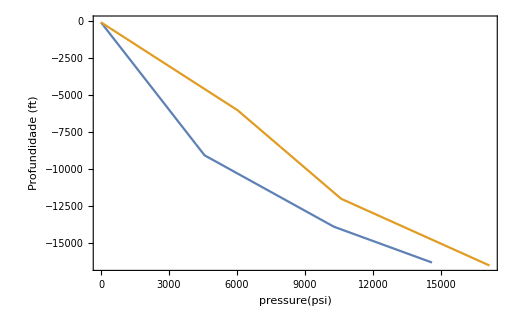

```mathematica
dataporepressure={{0,-100},{4568.32,-9066},{10278.50,-13885},{14606.48,-16300}};
PtsFracPressure={{0,-100},{6025.97,-6025.97},{10597.39,-12000},{17142.84,-16500}};
tabpore=Table[{Interpolate[y,dataporepressure],y},{y,-16300,0}];
tabfrac=Table[{Interpolate[y,PtsFracPressure],y},{y,-16500,0}];
ListLinePlot[{tabpore,tabfrac},Frame->True,FrameLabel->{{" Profundidade (ft) "," "},{"pressure(psi)"," Janela Operacional "}},LabelStyle->Directive[Bold,14],Axes->None]
```

```mathematica
Interpolate[-9700,dataporepressure]
```

5319.57